# 1. DN - Računalniška orodja v matematiki

#### 1. Analiza z mathematico

Točke od a do j rešite točno in tudi numerično.

a. Definirajte funkcijo .

```mathematica
f[x_] :=  (E^(x+3))/(100x+2)
```

b. Izračunajte definicijsko območje funkcije .

```mathematica
FunctionDomain[f[x],x]
```

x<-1/50||x>-1/50

c. Izračunajte limite funkcije  na robovih definicijskega območja.

```mathematica
Limit[f[x], x->-1/50,Direction->"FromAbove"]
Limit[f[x], x->-1/50,Direction->"FromBelow"]
```

∞

-∞

d. Izračunajte odvod funkcije .

```mathematica
f'[x]
```

-(100 ⅇ^(3+x))/(2+100 x)^2+ⅇ^(3+x)/(2+100 x)

e. Izračunajte lokalne ekstreme funkcije .

```mathematica
SolveValues[f'[x]==0,x]
```

{49/50}

f. Izračunajte intervale naraščanja in padanja funkcije .

```mathematica
Reduce[f'[x]>0, x]
Reduce[f'[x]<0, x]
```

x>49/50

x<-1/50||-1/50<x<49/50

g. Narišite graf funkcije  na intervalu [-5, 5].

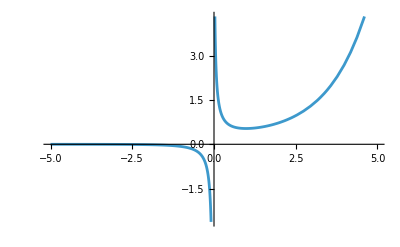

```mathematica
Plot[f[x],{x,-5,5}]
```

h. Določite zalogo vrednosti funkcije .

```mathematica
FunctionRange[f[x],x,y]
```

y<0||y≥ⅇ^(199/50)/100

i. Izračunajte nedoločeni integral funkcije .

```mathematica
Simplify[Integrate[f[x],x]]
```

1/100 ⅇ^(149/50) ExpIntegralEi[1/50+x]

j. Na 3 decimalke natančno izračunajte volumen vrtenine , ki jo dobimo, če graf funkcije  zavrtimo okoli  osi na intervalu [0.5, 2]. Vrtenino tudi narišite.

```mathematica
Integrate[2 Pi x(f[x]), {x,0.5,2}]
```

```mathematica
RevolutionPlot3D[f[x],{x,0.5,2},RevolutionAxis->{1, 0, 0}]
```

-Graphics3D-

#### 2. Splošno o mathematici

a. Pobrišite vrednost vseh spremenljivk, ki ste jih uporabili v prejšnji nalogi.

```mathematica
Clear[f]
```

b. Definirajte funkcijo  in izračunajte njeno vrednost v vseh celih številih med 1 in 100.

```mathematica
g[x_]:=(1+x^2.1)/3+x
tab = g/@Table[i,{i, 1, 100}]
```

{1.66667,3.76236,6.6817,10.4597,15.1218,20.6881,27.1753,34.5977,42.9681,52.2975,62.5963,73.8736,86.1381,99.3977,113.66,128.931,145.219,162.529,180.866,200.238,220.648,242.102,264.605,288.162,312.777,338.454,365.198,393.012,421.901,451.868,482.917,515.052,548.275,582.591,618.002,654.512,692.124,730.841,770.665,811.6,853.649,896.814,941.098,986.504,1033.03,1080.69,1129.48,1179.39,1230.44,1282.63,1335.96,1390.42,1446.03,1502.79,1560.69,1619.75,1679.95,1741.31,1803.82,1867.49,1932.32,1998.32,2065.47,2133.79,2203.28,2273.94,2345.76,2418.76,2492.94,2568.29,2644.82,2722.52,2801.41,2881.48,2962.74,3045.18,3128.8,3213.62,3299.63,3386.83,3475.22,3564.81,3655.59,3747.57,3840.75,3935.13,4030.72,4127.51,4225.5,4324.7,4425.1,4526.72,4629.54,4733.58,4838.83,4945.29,5052.97,5161.86,5271.98,5383.31}

c.  Iz seznama dobljenega v nalogi b. izberite zgolj tiste vrednosti, ki imajo na mestu enic praštevilo. Pomagajte si s _?PrimeQ in MemberQ.

```mathematica
Select[tab, PrimeQ[Mod[Floor[#], 10]]&]
```

{3.76236,15.1218,27.1753,42.9681,52.2975,62.5963,73.8736,113.66,145.219,162.529,242.102,312.777,365.198,393.012,482.917,515.052,582.591,692.124,853.649,1033.03,1282.63,1335.96,1502.79,1803.82,1867.49,1932.32,2065.47,2133.79,2203.28,2273.94,2345.76,2492.94,2722.52,2962.74,3045.18,3213.62,3475.22,3655.59,3747.57,3935.13,4127.51,4225.5,4425.1,4733.58,4945.29,5052.97,5383.31}

d. Definirajte anonimno funkcijo, ki kvadrira število in mu prišteje 1 in jo uporabite na zgoraj dobljenem seznamu.

```mathematica
#^2 + 1&/@%31
```

{15.1554,229.67,739.497,1847.25,2736.03,3919.29,5458.31,12919.5,21089.5,26416.5,58614.5,97830.5,133371.,154460.,233210.,265279.,339413.,479036.,728718.,1.06716×10^6,1.64514×10^6,1.78478×10^6,2.25838×10^6,3.25377×10^6,3.48753×10^6,3.73387×10^6,4.26617×10^6,4.55307×10^6,4.85444×10^6,5.17079×10^6,5.50261×10^6,6.21474×10^6,7.41213×10^6,8.77781×10^6,9.2731×10^6,1.03274×10^7,1.20772×10^7,1.33633×10^7,1.40443×10^7,1.54853×10^7,1.70363×10^7,1.78548×10^7,1.95815×10^7,2.24068×10^7,2.44559×10^7,2.55325×10^7,2.898×10^7}

e. Seznam iz prejšnje naloge zaokrožite navzdol in seštejte vsa tista števila, ki so deliva s 3.

```mathematica
Total[Select[Floor/@%35, Divisible[#,3]&]]
```

62338386

#### 3. Prepisovalna pravila

```mathematica
Clear[x, y, izraz]
izraz = x^2 + 2x + 1
```

1+2 x+x^2

a. Definirajte prepisovalno pravilo, ki  v izrazu vse pojavitve x zamenja z y + 1.

```mathematica
izraz/.x->y+1
```

1+2 (1+y)+(1+y)^2

b. Z uporabo prepisovalnih pravil izračunajte vrednost izraza za  x = 2

```mathematica
izraz/.x->2
```

9

c. Definirajte funkcija  in s pomočjo prepisovalnih pravil zamenjajte vse pojavitve  v

```mathematica
f[x_]:=x^5- 4x^3 + x^2+3x-2
pravilo := x^n_ :> 2n x^(n-1)
f[x]/.pravilo
```

-2+7 x-24 x^2+10 x^4

d. Prepisovalno pravilo iz naloge c uporabite na funkciji ,  kolikokrat gre.

```mathematica
g[x_] := x^2025
g[x]//.pravilo
```

25199184140713966109324439717615969231870192509490767849406134007669090502116720223690823433147324568647885368040234868472725805842375408382714777235818667370000750799297267165516298874435057056626391536083341407086034354955958682263835431941760258054719800578096972937396209464145334192241572534839256708511969052598930072305886602639853383101402921632069724373099652607563860160850638354922808087238654971425101774219020044811168483076705915245408528781053465765686959220085213595325825645754776086514408326545440195205062306924364036505664434061570848962327935913165722289654305888640209925133534626336635435505713127178633684044226041232941592119789855938477549383444472006212451101236135558501147068831093644865400379555901186021070326806533626279865761344623690356572746289168907516209675279484432401064230903437279808760641525685377825853870241756111471353448110147208868096793711163561246968674526934987540452806670537204928185295614192270273731457467374837359983703583401230885852625994172019545836838149058121805888171240017631456801775603021035657543659149163444642609687539227991190696727267788860964719327156982910859191950789849367397175125444831567800030133816248636423457266624421250450356817053841035971385518529511156063665481958342875766993473522734552131920882042790159489709367782626922853899994331466640086999257107852592255380908824028510340588409110195055344828312904113756071338420629068087780705473770891073051175947673764970164992457067216870404174595840737543458631743701439027616098635496855772885923778055855640998741624210083027605176696467062974342730283411372393019788121193931454258408612299649856674530132445979675277111530784584334555295902970365075863846099541939700411558791891099490349114132476289338444711572504507068090299291915601571575050265572475627652553496639688278685485555342994927947515099308806020923451047933680263532372896538915039567894982295608271133256339406694582248505444225175520618016319544052987304782315549530655299604854185657125263385350855383313053522930893826944501805788204889586232231621353947152688354554821348023754561140027652225557987424210217430078191652981018835977203349827791997397831755300842427118789974838452667556816096532477699694780692872081428909713256383684086382750143592718630822790249067628113971178996116661164429572214172021144362975718908758918732259975218610032068250154753671381289499363211212544918554906527649142488437195861743124110611926303643632698779566297831604891887835987792011711493576384051779164997450123928495755237903050176564773974822030345559458096535957217425346233313341864719926607048169573250121789292628743531525583151519953853207714722401963939375068669133067236386986610736363800474691883053455574817451572633328077457900898806425911050751058398907736533933621123555747082103950289922053851873681093991896403039447346523464443246126896873684738902265877309905368794616471261313192710762319162762012002603910076199681899236172438626194520869861899963221180140899239377138506230461881911245689387721475528983229254688544365596157373215610219473857547810833108800706959271748640488835316873641694943156345079373403970191946351280201608949230502646882698621138359976248410148678202760870095074301648275380751631601142449241653771118966448194547719799372734734031692400490534129976626834528845809425808424837609070734028016420510060062340404064432822758704778019389096222115383258516123777079703105970568984075791505716164023094125555618474249401192387487323754246341646559389480510119568107032478290624914121972104123840203726927317442187716594186176883824386859731670044440541024970794898822529547388912407173963601558682959647683671956321180111953756131184684927919134500950141740120023015207537020941616320702727375653965582417529819625736312978424624678898444025172880847484041102336158172901585880116664780154940235873064101225286918853544301958103010030433664324526269070704130937723936914626587611008323471127609260992234843864792650252141938328607454272561003752252856366773469367116134186676608342596589179005703376544813133598691984703814143762072038911008138691525788504937199002598544332739546339635656797495583303877052174036434903685773152746097316644292984960270880117462117199358078094111367293533508290728754178608632942285585330263397125938820295892987340799884603900201639124248078748845879706377746330339504844007218168672957359486135558499573267507805353805338403933393045636366390031361088501766633696152756952896652400268556897520591015662419941672049101786309437962568331143941413129075071968375648007955222657601566892219194143775712028182308005265314167645934013066614260441005838752448458024988242213676852256603205557535026588421324286976947261082959783514609345697265240824438845724170716073184732669005814417955499444896138379313404266063857739357041639184987944699944708217879228883080457826051467540255876343497072706560895764575185971409016110032210219156385648026347674108024600072382311953524546155148967805684860857607949990993168867685353782243877458251208450038181807541141510947441542697337277763057880611598299786062875780936930956206561811740587769326550029896504577429015345647880649529877837814476239548089240279527332717699252071115717138866472777289380550933609576620224718248487199508077504430637812751077562400775521499758225376549279427239888120476683801821824452573492598147838596922302766044903104404659569170135786978104632363575685371266783131742921697473898744826470650941268018722566862283484421476693506221646320637252536012883909963885278758019834783453161773625122316724183935090789804683103396398315627396539714108621338961678338783801504807156643947355924959150610515492030588427583339059655212279447542029241287957999448453335229072120444198588444728444336581297010699405097112586532110020192174295377779849092571877013774177096811122133993887552905538546342074962918078939389669103370450441524830799968561015054436233354196370942710662036190953335685120000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000 x

e. Definiraj prepisovalna pravila, s pomočjo katerih lahko izračunate poljuben člen fibonaccijevega zaporedja, z začetkom `Fib[10]`

```mathematica
Fib[n_] := Nest[Replace[{x_,y_}->{y,x+y}], {0,1}, n][[1]]
Fib[10]
```

55